```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==0.35^2,{n,-3,3},{m,-3,3}]]],{x,-3,3},{y,-3,3},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
(* test conditions: r0 = [0.24, -0.17], v0 = [-0.42, 0.23] *)
```

```mathematica
points:={{0.34, -0.27},{0.2648292258460074,-0.22883505224900402},{0.704886599217583,-0.811829649841864},{0.17883767052551303,-0.6991394216567955},{-0.14959985435302536,-0.3164172618198206},{-0.822754589319239,-0.30180136578983097},{-1.007197815492265,-0.6500740200383255},{-1.235337232813053,-0.25906830537889863},{-1.656080973795874,-0.06495924425980043},{-1.3468666022022222,-0.046728580940193484},{-1.6694775554026566,-0.11512998574391822},{-1.183609592687336,-0.7020276565296905},{-1.8027346029986315,0.7108869370888139},{-1.2894773855039479,0.19673038220314698},{-2.706932224160555,0.8086592600502589},{-2.1678068329440583,0.3071495837817162},{-2.248320323341356,0.7533483893917524}}
```

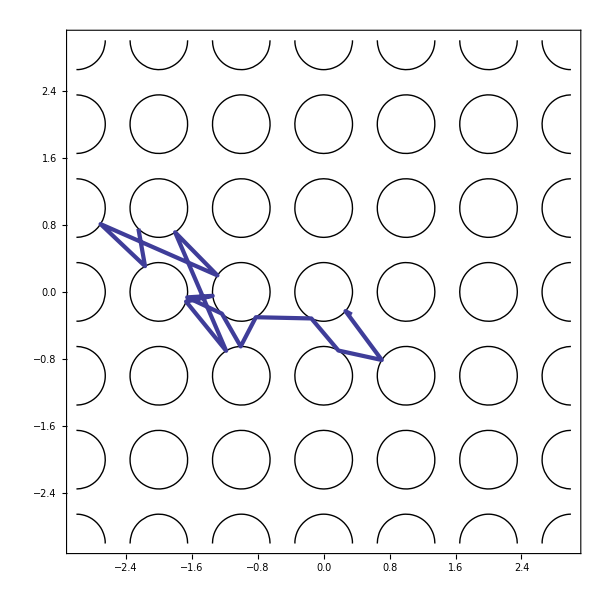

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```